# Mathematica: The Basics

© 2021 R.U. Gobithaasan All Rights Reserved.
R.U.Gobithaasan (2021). Scientific Computing, Lectures for Undergraduate Degree Program B.Sc (Applied Mathematics), Faculty of Ocean Engineering Technology, University Malaysia Terengganu.

References:
1. Michael Trott , The Mathematica GuideBook for Graphics  (2004, Springer-Verlag New York) 
2. Michael Trott - The Mathematica Guidebook for  Programming (2005, Springer)
3. Michael Trott - The Mathematica GuideBook for Symbolics  (2005, Springer)

## Mathematica Syntax

Basic operation:
- Shift+Enter   to run/evaluate
- Enter  to move to a new line in the same cell (a cell in indicated by a single vertical - bar/bracket on the right hand side)
- Click on an empty space or down button on your keyboard to create a new cell (a horizontal line will appear, just type when you see that line)
- Double click the RHS bracket to collapse the cell
- To quickly evaluate the entire notebook, at the top menu, click Evaluation>Evaluate notebook

### Palettes > BAsic Math Assistant

## Clear all stored values

```mathematica
ClearAll["Global`*"]
```

## Rules to remember

The first letter of ALL built-in functions and symbols is ALWAYS CAPITAL LETTER.

```mathematica
Abs[-10]
Integrate[y,y]
```

10

y^2/2

Brackets usage:
round - parenthesis
square - functions
curly - sets, range, lists, matrices

## Documentation

```mathematica
?Integrate
```

```mathematica
??Integrate
```

```mathematica
Information[Integrate]
```

# Numerical Computation

```mathematica
Head[3]
Head [3.3]
Head[3+2I]
Head[x]
```

Integer

Real

Complex

Symbol

```mathematica
Cos[Pi/5]
```

1/4 (1+√5)

```mathematica
N[Cos[Pi/5],100]
```

0.8090169943749474241022934171828190588601545899028814310677243113526302314094512248536036020946955687

```mathematica
NIntegrate[y^5,{y,0,3}]
```

121.5

## Define Variable

```mathematica
a=20;
```

```mathematica
a
```

20

```mathematica
a^(-1/2)
a*2
```

1/(2 √5)

40

```mathematica
b=Cos[3]+Log[2.6]+a
```

19.9655

```mathematica
a+b
```

39.9655

A defined variable will continue to hold its value (globally: even in a different notebook) until you change or clear it.

## Calling previous values

```mathematica
Clear[a,b,c,d]
```

```mathematica
a=4+b;
```

```mathematica
c=5+b;
```

```mathematica
d=b;
```

```mathematica
{%, %%}
```

{b,5+b}

```mathematica
%218
```

4+b

## To clear a variable or all variables

```mathematica
ClearAll[a]
a
```

a

```mathematica
a=20
ClearAll[a,b]
a
b
```

20

a

b

```mathematica
a=2;b=-3;c=9;(*use ";" to suppress outputs*)
a
b
c
```

2

-3

9

```mathematica
ClearAll["Global`*"](*Clear all the values*)
a
b
c
```

a

b

c

## Arithmetic Operations

```mathematica
1+2/3-8*9
```

-211/3

```mathematica
9.7^1.2
```

15.2801

### Some notes:

1) multiplication can be written in a few different ways: */space/()

```mathematica
a b
a*b
a(b)
```

a b

a b

a b

2) ways to write power: Shift+6 or Ctrl+6
3) ways to write divide: / or Ctrl+/
4) to write square root: use function “Sqrt[]” or Ctrl+2

## Some basic built in functions

### Three ways calling built-in function

```mathematica
{Abs[-10], Abs@-10,-10//Abs}
```

{10,10,10}

```mathematica
N[1/3](*default significant figures = 6*)
N[π,8](*Shows π value with 8 significant figures*)
```

0.333333

3.1415927

```mathematica
Exp[3](*Exponent*)
Log[3]
Log[3]//N
N[Log[3]]
```

ⅇ^3

Log[3]

1.09861

1.09861

### Trigonometry

Mathematica uses radians by default

```mathematica
Cos[30]//N
```

0.154251

use “Degree” to convert values to radians, i.e. 30 Degree to radians:

```mathematica
Cos[30Degree]//N
```

0.866025

```mathematica
{Cos[30Degree],Sin[30Degree],Tan[30Degree]}
```

{(√3)/2,1/2,1/(√3)}

# Symbolic Computations

### Algebraic operation

```mathematica
Head[x]
```

Symbol

```mathematica
Clear[a,b]
b+a+a
```

2 a+b

```mathematica
ReplaceAll[2a+b,{a-> 1,b-> 0}]
```

2

```mathematica
2a+b/. {a-> 1,b-> 0}
```

2

```mathematica
3a+1.3b+6/7 b
```

3 a+2.15714 b

```mathematica
g=Factor[(-768 t Cos[2 t]+48 t Cos[4 t]+384 (-1+2 t^2) Sin[2 t]-12 (-1+8 t^2) Sin[4 t]+4 t (72 t^2+2 (96-64 t^2) Cos[2 t]+4 (-3+8 t^2) Cos[4 t]-128 t Sin[2 t]+16 t Sin[4 t])+4 (24 t^3+(96-64 t^2) Sin[2 t]+(-3+8 t^2) Sin[4 t]))/1024]
```

-1/8 t^3 (-3+4 Cos[2 t]-Cos[4 t])

```mathematica
Expand[g]
```

(3 t^3)/8-1/2 t^3 Cos[2 t]+1/8 t^3 Cos[4 t]

```mathematica
?FullSimplify
```

```mathematica
FullSimplify[g]
```

t^3 Sin[t]^4

```mathematica
FullSimplify[25 q^2+67q+q s+s^2]
```

25 q^2+s^2+q (67+s)

```mathematica
Reduce[x^2-y^3==1,{y}]
```

y==(-1+x^2)^(1/3)||y==-(-1)^(1/3) (-1+x^2)^(1/3)||y==(-1)^(2/3) (-1+x^2)^(1/3)

```mathematica
Trace[%]
```

{%,Out[$Line-1],{{$Line,334},334-1,333},%333,y==(-1+x^2)^(1/3)||y==-(-1)^(1/3) (-1+x^2)^(1/3)||y==(-1)^(2/3) (-1+x^2)^(1/3)}

```mathematica
Solve[x^2+a x+1==0,x]
```

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

Functions like FullSimplify and Factor are called “Built-in Functions”. They are predefined functions that are written in the Mathematica programme.

### Differentiation (Look up “D” or “differentiation” in documentation center for more info)

```mathematica
?D
```

RowBox[{"D", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["x", "TI"]}], "]"}] gives the partial derivative RowBox[{"∂", StyleBox["f", "TI"], "/", "∂", StyleBox["x", "TI"]}]. 
RowBox[{"D", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["n", "TI"]}], "}"}]}], "]"}] gives the multiple derivative RowBox[{SuperscriptBox["∂", StyleBox["n", "TI"]], StyleBox["f", "TI"], "/", "∂", SuperscriptBox[StyleBox["x", "TI"], StyleBox["n", "TI"]]}]. 
RowBox[{"D", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "]"}] differentiates StyleBox["f", "TI"] successively with respect to RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}].
RowBox[{"D", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "}"}]}], "]"}] for a scalar StyleBox["f", "TI"] gives the vector derivative RowBox[{"(", RowBox[{RowBox[{"∂", RowBox[{StyleBox["f", "TI"], "/", RowBox[{"∂", SubscriptBox[StyleBox["x", "TI"], "1"]}]}]}], ",", RowBox[{"∂", RowBox[{StyleBox["f", "TI"], "/", RowBox[{"∂", SubscriptBox[StyleBox["x", "TI"], "2"]}]}]}], ",", "…"}], ")"}]. 
RowBox[{"D", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", StyleBox["array", "TI"], "}"}]}], "]"}] gives a tensor derivative.

```mathematica
D[Cos[x],x]
```

-Sin[x]

```mathematica
D[x^3,x]
```

3 x^2

```mathematica
D[x^3,{x,2}](*second derivative*)
```

6 x

```mathematica
D[x^3+y,x](*partial*)
```

3 x^2

### Integration (Look up “integrate” in documentation center for more info)

```mathematica
?Integrate
```

RowBox[{"Integrate", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["x", "TI"]}], "]"}] gives the indefinite integral RowBox[{"∫", StyleBox["f", "TI"], " ", StyleBox["d", "TI"], StyleBox["x", "TI"]}]. 
RowBox[{"Integrate", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] gives the definite integral RowBox[{SubsuperscriptBox["∫", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]], " ", StyleBox["f", "TI"], " ", StyleBox["d", "TI"], StyleBox["x", "TI"]}]. 
RowBox[{"Integrate", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] gives the multiple integral RowBox[{SubsuperscriptBox["∫", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]], RowBox[{StyleBox["d", "TI"], StyleBox["x", "TI"], RowBox[{SubsuperscriptBox["∫", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]], RowBox[{StyleBox["d", "TI"], "", StyleBox["y", "TI"], " ", "…", " ", StyleBox["f", "TI"]}]}]}]}].

```mathematica
Integrate[x,x]
```

x^2/2

```mathematica
Integrate[x y,x]
```

(x^2 y)/2

```mathematica
Integrate[t^3 Sin[t]^4,t]
```

(-192 (-1+2 t^2) Cos[2 t]+3 (-1+8 t^2) Cos[4 t]+4 t (24 t^3+(96-64 t^2) Sin[2 t]+(-3+8 t^2) Sin[4 t]))/1024

```mathematica
Integrate[Exp[-3t]*t^(2/5),{t,1,Infinity}]
```

ExpIntegralE[-2/5,3]

# Defining functions

### f(x)=sin(x^2)

```mathematica
f[x_]:=Sin[x^2]
```

```mathematica
?f
```

#### Calling functions and evaluating functions at certain points

```mathematica
f[x]
```

Sin[x^2]

```mathematica
f[a+3]
```

Sin[(3+a)^2]

```mathematica
f[b]
```

Sin[b^2]

```mathematica
f[π]//N
```

-0.430301

### Multivariable function g(x,y)=e^x+x y

```mathematica
Clear[g]
g[x_,y_]:=Exp[x]+x y
```

```mathematica
?g
```

#### Calling functions and evaluating functions at certain points

```mathematica
g[x,y]
```

ⅇ^x+x y

```mathematica
g[2,8]
```

16+ⅇ^2

The underscores behind the variables are compulsory when defining functions, but are not needed when calling them. We CANNOT define a function with g[x]:=x.
The function definitions will remain until you clear or change it.

```mathematica
Clear[h]
h[x_][y_]:= Exp[x]+x y
h[2][8]
```

16+ⅇ^2

### setting conditions for the input

```mathematica
Clear[f1]
f1[x_Integer]:=x*x
```

```mathematica
{f1[],f1[3],f1[3.2]}
```

{f1[],9,f1[3.2]}

### More than a variable as input

```mathematica
Clear[f2]
```

```mathematica
f2[x__]:=x*x
```

```mathematica
{f2[],f2[{2,3}]}
```

{f2[],{4,9}}

```mathematica
f2[{4.3,5.3,6.3}]
```

{18.49,28.09,39.69}

### Deleting function definition

```mathematica
ClearAll["Global`*"](*will clear all the variables and functions*)
```

# Plotting

### Points

### Plotting a series of points (Cartesian coordinates)

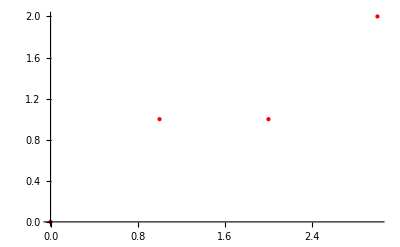

```mathematica
ListPlot[{{0,0},{1,1},{2,1},{3,2}},PlotStyle->{PointSize[Large],Red}]
```

### You can “store” all the plot as well

```mathematica
P={{0,0},{1,1},{2,1},{3,2}};
fig1=ListPlot[P,PlotStyle->{PointSize[Large],Red}];
```

```mathematica
fig1
```

-Graphics-

Other than “ListPlot”, we can opt for “Graphics” (“Graphics” do not display axes):

### Connecting the points with straight lines

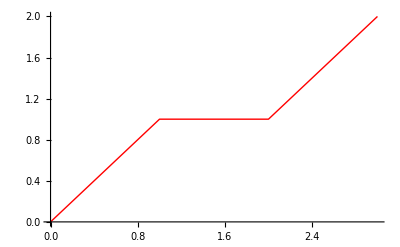
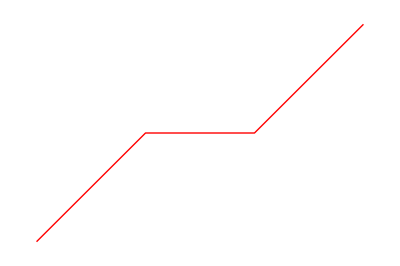
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListPlot[{{0,0},{1,1},{2,1},{3,2}},PlotStyle->{Thick,Red},Joined->True],ListLinePlot[{{0,0},{1,1},{2,1},{3,2}},PlotStyle->{Thick,Red}],Graphics[{Red,Thick,Line[P]}]}
```

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→Automatic,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,IntervalMarkers→Automatic,IntervalMarkersStyle→Automatic,Joined→False,LabelingFunction→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Overlaid,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

### Explicit Function

### 2D plot

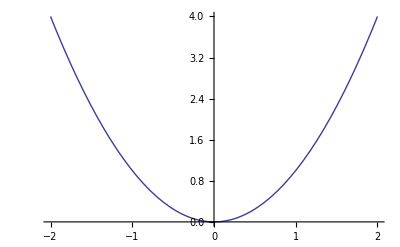

```mathematica
Plot[x^2,{x,-2,2}]
```

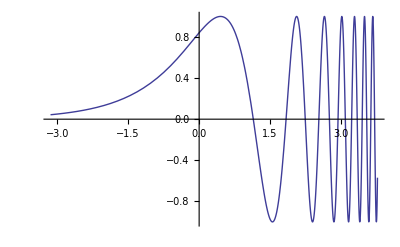

```mathematica
f[x_]:=Sin[Exp[x]]
Plot[f[x],{x,-π,1.2π}]
```

### Editing Plot (Colour, Axes, etc.)

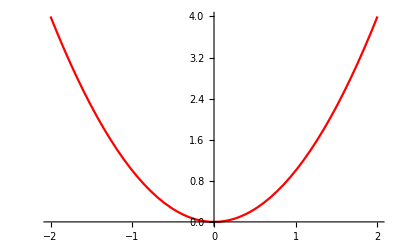
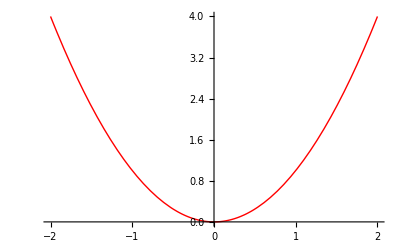
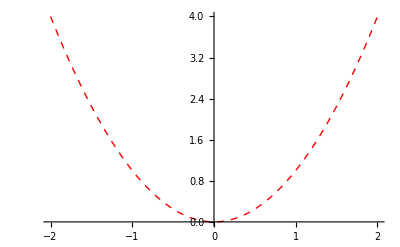
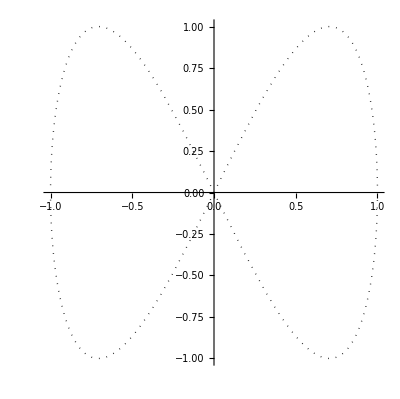

```mathematica
{Plot[x^2,{x,-2,2},PlotStyle->Red],Plot[x^2,{x,-2,2},PlotStyle->{Red,Thick}],Plot[x^2,{x,-2,2},PlotStyle->{Red,Thick,Dashed}],ParametricPlot[{Sin[t],Sin[2t]},{t,0,2Pi},PlotStyle->{Black,Dotted,Thick}]}
```

### Combining two graphs

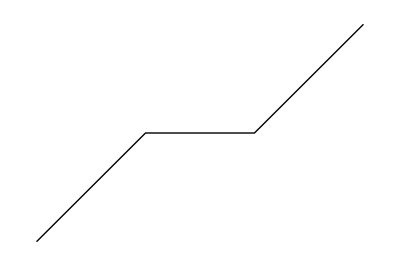
{-Graphics-,-Graphics-}

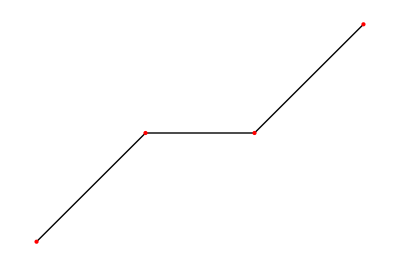

```mathematica
{figure1=Graphics[{Red,PointSize[Large],Point[P]}],figure2=Graphics[{Black,Thick,Line[P]}]}
Show[figure2,figure1]
```

### 3D Plot

```mathematica
g[x_,y_]:=Cos[x]Sin[y]
Plot3D[g[x,y],{x,0,2π},{y,0,2π}]
```

-Graphics3D-

### Parametric Plot

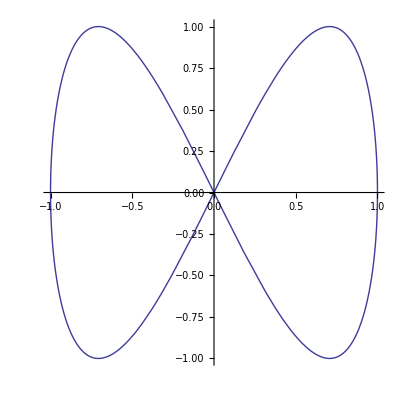

```mathematica
ParametricPlot[{Sin[t],Sin[2t]},{t,0,2Pi}]
```

```mathematica
ParametricPlot3D[{Cos[t] (3+Cos[u]),Sin[t] (3+Cos[u]),Sin[u]},{t,0,2Pi},{u,0,2Pi}]
```

-Graphics3D-

# Simulation and Animation

```mathematica
Clear[g,a,b,x,y]
g[x_,y_,a_,b_]:=(a Cos[a x]Sin[b y])/b
Manipulate[Plot3D[g[x,y,a,b],{x,0,2π},{y,0,2π}], {a,-3,3},{b,0.01,3}]
```

# Vectors and Matrices

### Lists is a n-tuple: order matters

```mathematica
list1={1,2,3,4,5,6}; 
list2={6,5,4,3,2,1};
list3={1,2,3,4,5,6}; 
list4={6,2,3,4,5,1};
```

```mathematica
list1==list3
```

True

### List properties

```mathematica
list1==list4
```

False

```mathematica
list1[[3]]
```

3

```mathematica
list1[[1;;3]]
```

{1,2,3}

### Simple List Operation

```mathematica
Length[list1]
```

6

```mathematica
2 *list1
```

{2,4,6,8,10,12}

```mathematica
list1+list2
```

{7,7,7,7,7,7}

```mathematica
√list2
```

{√6,√5,2,√3,√2,1}

```mathematica
{1,2,3,4,5}+{2,5,7,8,4}/{a,4,6,y,7}
```

{1+2/a,13/4,25/6,4+8/y,39/7}

### Generate a list using “Table[]”

```mathematica
Table[i,{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[Cos[2i],{i,1,10}]
```

{Cos[2],Cos[4],Cos[6],Cos[8],Cos[10],Cos[12],Cos[14],Cos[16],Cos[18],Cos[20]}

```mathematica
Table[i*j,{i,1,2},{j,1,2}]
```

{{1,2},{2,4}}

### Vector

```mathematica
v1={1,3};
v2={-2,6};
v3= {3,1}
```

{3,1}

```mathematica
v1==v3
```

False

### Simple Vector Operations

```mathematica
q=2;r=7;
```

```mathematica
q v1-r v2
```

{16,-36}

### Matrices

```mathematica
A={{1,2},{a,b}}
B={{1,2,3},{a,b,c},{2a,3b,4c}}
```

{{1,2},{a,b}}

{{1,2,3},{a,b,c},{2 a,3 b,4 c}}

### Showing Matrices in Standard Form

```mathematica
MatrixForm[A]
```

(1 | 2
a | b)

```mathematica
MatrixForm[B]
```

(1 | 2 | 3
a | b | c
2 a | 3 b | 4 c)

### Size of a Matrix

```mathematica
Dimensions[M]
```

{3,1}

```mathematica
Dimensions[A]
```

{2,2}

### Simple Matrix Operations

```mathematica
A.B(*Example of problem usually encountered*)
```

Dot::dotsh: Tensors {{1,2},{a,b}} and {{1,2,3},{a,b,c},{2 a,3 b,4 c}} have incompatible shapes.

{{1,2},{a,b}}.{{1,2,3},{a,b,c},{2 a,3 b,4 c}}

```mathematica
M={{6},{4},{2}}
```

{{6},{4},{2}}

```mathematica
B*M (*Example of incorrect usage*)
```

Thread::tdlen: Objects of unequal length in {1,2,3} {6} cannot be combined.

Thread::tdlen: Objects of unequal length in {a,b,c} {4} cannot be combined.

Thread::tdlen: Objects of unequal length in {2 a,3 b,4 c} {2} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{{6} {1,2,3},{4} {a,b,c},{2} {2 a,3 b,4 c}}

```mathematica
U=B.M
MatrixForm[B.M]
```

{{20},{6 a+4 b+2 c},{12 a+12 b+8 c}}

(20
6 a+4 b+2 c
12 a+12 b+8 c)

```mathematica
4U
MatrixForm[%]
```

{{80},{4 (6 a+4 b+2 c)},{4 (12 a+12 b+8 c)}}

(80
4 (6 a+4 b+2 c)
4 (12 a+12 b+8 c))

```mathematica
4U-M
MatrixForm[4U-M]
```

{{74},{-4+4 (6 a+4 b+2 c)},{-2+4 (12 a+12 b+8 c)}}

(74
-4+4 (6 a+4 b+2 c)
-2+4 (12 a+12 b+8 c))

### GETTING PART OF A LIST/MATRIX

```mathematica
A={{1,2,3},{a,z,b}};
```

```mathematica
A[[1]]
```

{1,2,3}

```mathematica
A[[2]]
```

{a,z,b}

```mathematica
A[[2,2]]
```

z

```mathematica
A[[2,2;;3]]
```

{z,b}

## END